```mathematica
Clear[f]
N[(3*10^8*100*10^(-6))/(4*Pi*10^(-7)*100*10^6)*√((3*377)/(16*Pi*85*10^(-3)))]
```

3884.17

```mathematica
N[(3*10^8*100*10^(-6))/(4*Pi*10^(-7)*100*10^6)*√((3*377)/(16*Pi*50))]
```

160.148

```mathematica
amp=(3*10^8*100*10^(-6))/(4*Pi*10^(-7)*f)*√((3*377)/(16*Pi*50))
```

(1875000000 √2262)/(f π^(3/2))

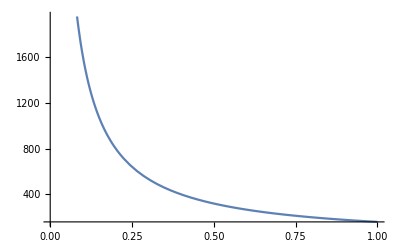

```mathematica
Plot[amp,{f,100*10^3,100*10^6}]
```

```mathematica
Rrad=(8*4*Pi*10^(-7)*Pi^3*(5*10^(-5))^2*(f)^4)/(3*(3*10^8)^3)
N[(8*4*Pi*10^(-7)*Pi^3*(5*10^(-5))^2*(100*10^6)^4)/(3*(3*10^8)^3)]
```

(f^4 π^4)/10125000000000000000000000000000000000000

9.62065×10^-7

```mathematica
Rdc=(1.68*10^(-8)*50*10^(-3))/((500*10^(-6))^2)
```

0.00336

```mathematica
Rac=(50*10^(-3))/(Pi*500*10^(-6))Sqrt[Pi*4*Pi*10^(-7)*f*1.68*10^(-8)]
(50*10^(-3))/(Pi*500*10^(-6))Sqrt[Pi*4*Pi*10^(-7)*100*10^6*1.68*10^(-8)]
```

8.19756×10^-6 √f

0.0819756

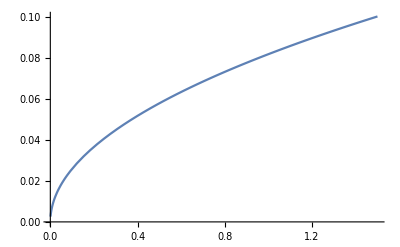

```mathematica
Plot[Rac,{f,100*10^3,150*10^6}]
```

```mathematica
R=Rrad+Rdc+Rac
```

0.00336+8.19756×10^-6 √f+(f^4 π^4)/10125000000000000000000000000000000000000

```mathematica
ampR=(3*10^8*100*10^(-6))/(4*Pi*10^(-7)*f)*√((3*377)/(16*Pi*R))
```

(18750000000 √1131 √(1/(0.00336+8.19756×10^-6 √f+(f^4 π^4)/10125000000000000000000000000000000000000)))/(f π^(3/2))

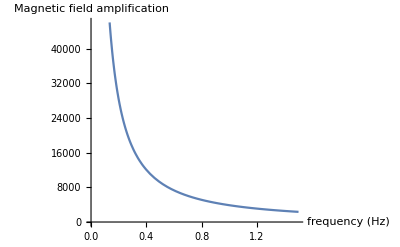

```mathematica
Plot[ampR,{f,100*10^3,150*10^6},AxesLabel->{"frequency (Hz)","Magnetic field amplification"}]
```

```mathematica
f=100*10^6
ampR
```

100000000

3876.5

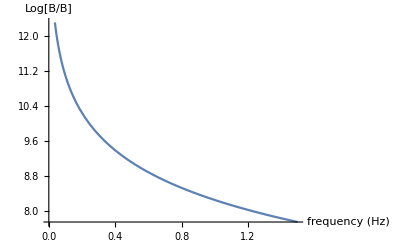

```mathematica
Plot[Log[ampR],{f,100*10^3,150*10^6},AxesLabel->{"frequency (Hz)","Log[B/B]"}]
```

```mathematica
(*DISTANCE CALCULATION*)
Clear[f,R]
c=3.0*10^8;
Z=377;
A=(5*10^(-3)*10*10^(-3));
L=50*10^(-3);
a=Pi*((500*10^(-6))/2)^2;
rho=1.68*10^(-8);

Rrad=(8 mu Pi^3 A^2 f^4)/(3 c^3);
Rdc=(rho L)/a;
Rac=L/(Pi (500*10^(-6)))Sqrt[Pi mu f rho];

R=Rrad+Rdc+Rac;
mu=4*Pi*10^(-7);
alpha=100*10^(-6);
kb=1.3807×10^(−23);
T=23.4*10^5;
df=1;

k=11.25*10^(-7);

Bnoise=(4 mu f)/c Sqrt[(Pi 4 kb T df)/(3 Z)];
Bsens=10*10^(-12);
Bext=(Bsens+Bnoise)(mu f)/(c alpha)Sqrt[(16 Pi R)/(3 Z)];
d=Sqrt[k/Bext];
d;

f=27*10^6;

R
d
```

0.0468739

46683.1

```mathematica
Clear[f,R,Rrad,Rdc,Rac](*checking why Harry calc is wrong*)
c=3.0*10^8;
Z=377;
A=(5*10^(-3)*10*10^(-3));
L=50*10^(-3);
a=Pi*((500*10^(-6))/2)^2;
rho=1.68*10^(-8);


Rrad=(8 mu Pi^3 A^2 f^4)/(3 c^3);
Rdc=(rho L)/a;
Rac=L/(Pi (500*10^(-6)))Sqrt[Pi mu f rho];

(*R=Rrad+Rdc+Rac;*)
R=0.085;
mu=4*Pi*10^(-7);
alpha=100*10^(-6);
kb=1.3807×10^(−23);
T=23.4*10^5;
df=1;

k=11.25*10^(-7);

Bnoise=(4 mu f)/c Sqrt[(Pi 4 kb T df)/(3 Z)];
Bsens=10*10^(-12);
Bext=(Bsens+Bnoise)(mu f)/(c alpha)Sqrt[(16 Pi R)/(3 Z)];
d=Sqrt[k/Bext];
d;
f=27*10^6;
R;(*he didnt take into account the resistances frequency dependance*)
d
```

40228.9

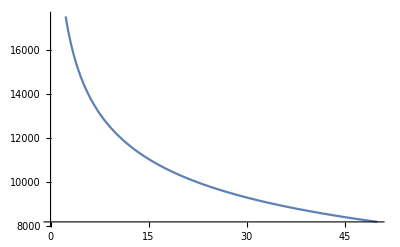

```mathematica
(*DISTANCE CALCULATION with added DC resistance*)
Clear[f,R]
c=3.0*10^8;
Z=377;
A=(5*10^(-3)*10*10^(-3));
L=50*10^(-3);
a=Pi*((500*10^(-6))/2)^2;
rho=1.68*10^(-8);

Rrad=(8 mu Pi^3 A^2 f^4)/(3 c^3);
Rdc=(rho L)/a+Rcomp;
Rac=L/(Pi (500*10^(-6)))Sqrt[Pi mu f rho];

R=Rrad+Rdc+Rac;
mu=4*Pi*10^(-7);
alpha=100*10^(-6);
kb=1.3807×10^(−23);
T=23.4*10^5;
df=1;

k=11.25*10^(-7);

Bnoise=(4 mu f)/c Sqrt[(4 kb T df)/(3 Z)];
Bsens=10*10^(-12);
Bext=(Bsens+Bnoise)(mu f)/(c alpha)Sqrt[(16 Pi R)/(3 Z)];
d=Sqrt[k/Bext];
d;

f=27*10^6;

R;
d;
Plot[d,{Rcomp,0,50}] (*distance of drone detection vs added resistor*)
```

```mathematica
dfclass=10*10^3;

Bclass=(4 mu f)/c Sqrt[(Pi 4 kb T dfclass)/(3 Z)];

dclass=Sqrt[k/Bclass]
```

6442.5

```mathematica
(d/dclass)*100-100
```

-100+337.163/(0.0468739+Rcomp)^(1/4)

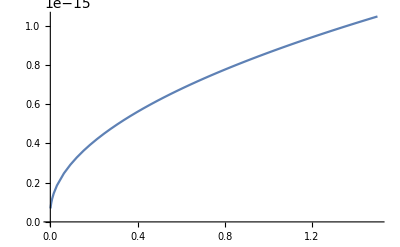

```mathematica
Clear[f]
II=(10*10^(-12))/(100*10^(-6));
Rcomp=0;
P=II^2 R;
R;
Plot[P,{f,100*10^3,150*10^6}]
```

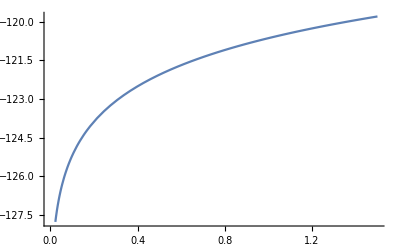

```mathematica
Pdbm=10Log[10,P]+30;
Plot[Pdbm,{f,100*10^3,150*10^6}]
```

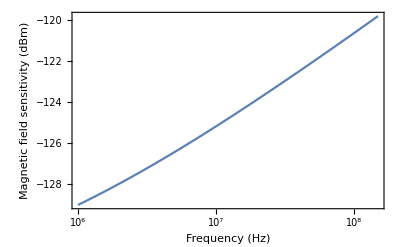

```mathematica
LogLinearPlot[Pdbm,{f,1*10^6,150*10^6},Frame->{True,True,False,False},FrameLabel->{"Frequency (Hz)","Magnetic field sensitivity (dBm)"}]
```

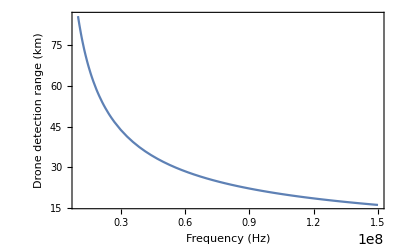

```mathematica
(*DISTANCE CALCULATION*)
Clear[f,R]
c=3.0*10^8;
Z=377;
A=(5*10^(-3)*10*10^(-3));
L=50*10^(-3);
a=Pi*((500*10^(-6))/2)^2;
rho=1.68*10^(-8);

Rrad=(8 mu Pi^3 A^2 f^4)/(3 c^3);
Rdc=(rho L)/a;
Rac=L/(Pi (500*10^(-6)))Sqrt[Pi mu f rho];

R=Rrad+Rdc+Rac;
mu=4*Pi*10^(-7);
alpha=100*10^(-6);
kb=1.3807×10^(−23);
T=23.4*10^5;
df=1;

k=11.25*10^(-7);

Bnoise=(4 mu f)/c Sqrt[(Pi 4 kb T df)/(3 Z)];
Bsens=10*10^(-12);
Bext=(Bsens+Bnoise)(mu f)/(c alpha)Sqrt[(16 Pi R)/(3 Z)];
d=Sqrt[k/Bext];
d;

Plot[d/1000,{f,10*10^6,150*10^6},Frame->{True,True,False,False},FrameLabel->{"Frequency (Hz)","Drone detection range (km)"}]
```

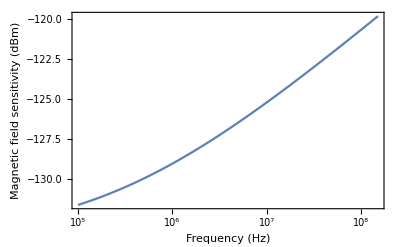

```mathematica
LogLinearPlot[Pdbm,{f,0.1*10^6,150*10^6},Frame->{True,True,False,False},FrameLabel->{"Frequency (Hz)","Magnetic field sensitivity (dBm)"}]
```

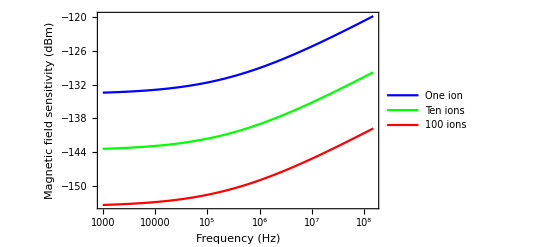

```mathematica
Clear[f]
II=(10*10^(-12)*(1/Sqrt[n]))/(100*10^(-6));
Rcomp=0;
n={1,10,100};
P=II^2 R;
R;
Pdbm=10Log[10,P]+30;
Pdbm[[1]];
one=LogLinearPlot[Pdbm[[1]],{f,0.001*10^6,150*10^6},Frame->{True,True,False,False},FrameLabel->{"Frequency (Hz)","Magnetic field sensitivity (dBm)"},PlotLegends->{"One ion"},PlotStyle->{Blue}];
ten=LogLinearPlot[Pdbm[[2]],{f,0.001*10^6,150*10^6},PlotLegends->{"Ten ions"},PlotStyle->{Green}];
hundred=LogLinearPlot[Pdbm[[3]],{f,0.001*10^6,150*10^6},PlotLegends->{"100 ions"},PlotStyle->{Red}];
Show[one,ten,hundred,PlotRange->All]
```

```mathematica
one=LogLinearPlot[Pdbm,{f,0.001*10^6,150*10^6},Frame->{True,True,False,False},FrameLabel->{"Frequency (Hz)","Magnetic field sensitivity (dBm)"},PlotLegends->{"One ion"},PlotStyle->Red];
Pdbm10=Pdbm*1/(Sqrt[10]);
ten=LogLinearPlot[Pdbm10,{f,0.001*10^6,150*10^6},Frame->{True,True,False,False},FrameLabel->{"Frequency (Hz)","Magnetic field sensitivity (dBm)"},PlotLegends->{"Ten ions"},PlotStyle->Blue];
Pdbm100=Pdbm*1/(Sqrt[100]);
hundred=LogLinearPlot[Pdbm100,{f,0.001*10^6,150*10^6},Frame->{True,True,False,False},FrameLabel->{"Frequency (Hz)","Magnetic field sensitivity (dBm)"},PlotLegends->{"One hundred ions"},PlotStyle->Green];
Show[hundred,ten,one,PlotRange->All,PlotLegends->"Expressions"]
```